```mathematica
$Assumptions = {p > 0, lambda > 0};
p = 3;
lambda = 1/5;
fX[x_] = lambda^p*x^(p-1) *Exp[-lambda*x] / Gamma[p];
FX[x_] = Integrate[fX[t], {t,0,x}]
```

1-1/50 ⅇ^(-x/5) (50+x (10+x))

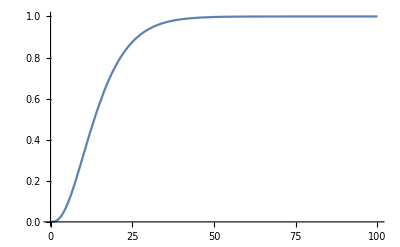

```mathematica
Plot[FX[x],{x, 0, 100}]
```

```mathematica
(*get the solved value, example*)
ss = x/.NSolve[FX[x] ==0.1, x, Reals][[1]]
```

5.51033

```mathematica
x1 = Range[0,99]/100;
x2 = {};
```

```mathematica
For[i=1, i <= Length[x1], i++, AppendTo[x2, x/.NSolve[FX[x] ==x1[[i]], x, Reals][[1]]]];
```

```mathematica
Map[Length,{{42.02973457442733},x},{1}]
```

{1,0}

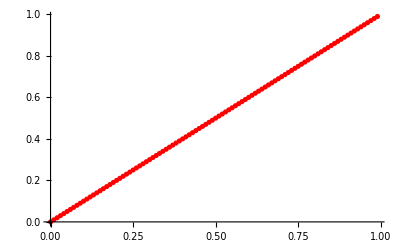

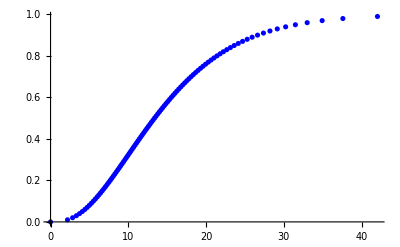

```mathematica
p1 = ListPlot[Transpose[{x1,x1}], PlotStyle->Red]
p2 = ListPlot[Transpose[{x2,x1}], PlotStyle->Blue]
```

```mathematica
Integrate[lambda*Exp[-lambda*t], {t,0,x}]
```

1-ⅇ^(-x/5)